## Shear Analysis

L: | 40.25
m: | 400
kappa: | 0.1
sigma: | 0.0002
kappa_sigma_r: | 500.
Delta: | 0.05025
Extension Minimum: | 0
Extension Maximum: | 150
beta: | 4.
mu: | 0.46
c: | 0.99
delta: | 6.45
b: | 1.
k: | 0.48
ev0: | 1.4
C0: | 0.37
e0: | 0.00375
beta: | 38.6817

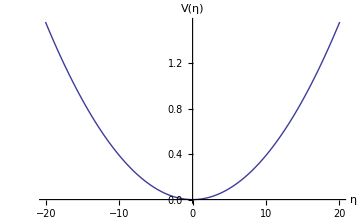

0.05025

Backbone spring constant κ:

0.1

Residue-pair spring constant σ(ϵ = 0.00375):

0.0002

κ/σ ratio:

500.

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]];
Needs["PlotLegends`"]
<<Units`
<<PhysicalConstants`

PotentialData = Import["potential_data.out","Table"];

PartitionFunction=Import["PartitionFunction_0_0.out","Table"];
FreeEnergy=Import["FreeEnergy_0_0.out","Table"];
dPartitionFunction=Import["dPartitionFunction_0_0.out","Table"];
dFreeEnergy=Import["dFreeEnergy_0_0.out","Table"];

Subscript[R, pfmxd]=Import["pfmxd_r.out","Table"];
Subscript[R, mxd]=Import["mxd_r.out","Table"];

Subscript[λ, pfmxd]=Import["pfmxd_lambda.out","Table"];
Subscript[λ, mxd]=Import["mxd_lambda.out","Table"];

Subscript[ρ, pfmxd]=Import["pfmxd_roe.out","Table"];
Subscript[ρ, mxd]=Import["mxd_roe.out","Table"];

Parameters=Import["Parameters"];
Grid[Parameters]
Needs["PlotLegends`"]
PlotPotentialData=ListLinePlot[{PotentialData},ImageSize->Medium,AxesOrigin->{0,0},AxesLabel->{Style["η",FontSize->18],Style["V(η)",FontSize->18]},PlotStyle->Thick,PlotRange->All]

ϵ=Parameters[[17,2]];
β=Parameters[[18,2]];

L=Parameters[[1,2]];
m=Parameters[[2,2]];
Δ=Parameters[[6,2]]
Print["Backbone spring constant κ:"]
κ=Parameters[[3,2]]
Print["Residue-pair spring constant σ(ϵ = "<>ToString[ϵ]<>"):"]
σ=Parameters[[4,2]]
Print["κ/σ ratio:"]
κσr=Parameters[[5,2]]
umax=Parameters[[7,2]];
umax=Parameters[[8,2]];

n=ToExpression[StringTrim[Last[StringSplit[Directory[],"/"]],RegularExpression["N*"]]];

fsTitle=24;
fsAxesLabel=18;
fs2=16;

Subscript[η, B]=4.0;

ToNewton=Convert[ElectronVolt/Angstrom,Newton] SI[Pico Newton]^-1;(*Converts eV/Å to pN*)
ToForceDimension[f_]:=(f (κ/(2β))^(1/2)) ToNewton;
ToDimension[η_]:=η ((κ β)/2)^(-1/2)(*Converts to Å*)
```

### Length Dimension Check

```mathematica
Subscript[η, B] (*No Dimension*)
ToDimension[Subscript[η, B]](*Å*)
```

4.

2.87622

### Force Dimension Check

```mathematica
0.5 (*No Dimension*)
σ ToDimension[Subscript[η, B]] ToNewton  (*pN*)
ToForceDimension[0.5] (*Converts force to dimensions of eV/Å then to J/m for pN*)
```

0.5

0.921643

28.8013

Partition function & Free Energy

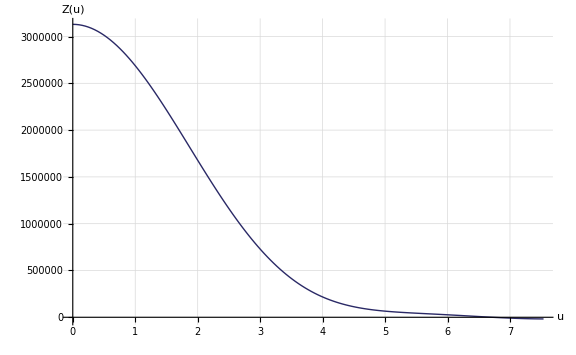
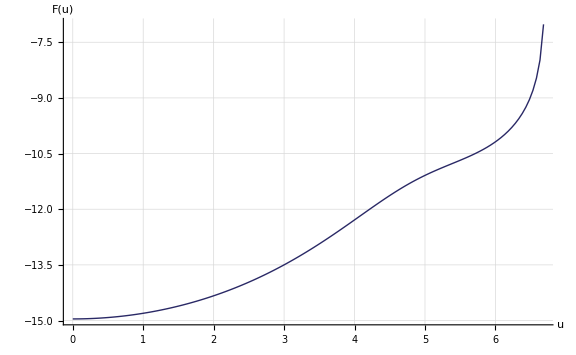

```mathematica
pIntactPF=ListLinePlot[PartitionFunction,ImageSize->Large,PlotStyle->{Thick,Darker[ColorData[1,1]]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["Z(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}];

pIntactFE=ListLinePlot[FreeEnergy,ImageSize->Large,PlotStyle->{Thick,Darker[ColorData[1,1]]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["F(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}];

{pIntactPF,pIntactFE}
```

Residue-pair separations (x-z), (x-y), (z-y)

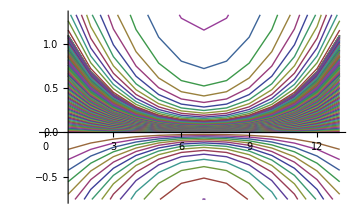
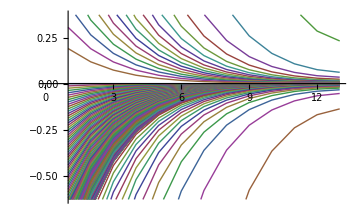

3.64111

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0124676 | 0.00777637 | 0.00488997 | 0.00313849 | 0.00211542 | 0.00158332 | 0.00141868 | 0.00158332 | 0.00211542 | 0.00313849 | 0.00488997 | 0.00777637 | 0.0124676
0.0249383 | 0.0155547 | 0.00978115 | 0.00627775 | 0.00423136 | 0.00316702 | 0.00283772 | 0.00316702 | 0.00423136 | 0.00627775 | 0.00978115 | 0.0155547 | 0.0249383
0.0374151 | 0.0233368 | 0.0146747 | 0.00941856 | 0.00634834 | 0.00475151 | 0.00425745 | 0.00475151 | 0.00634834 | 0.00941856 | 0.0146747 | 0.0233368 | 0.0374151
0.0499011 | 0.0311246 | 0.0195719 | 0.0125617 | 0.00846689 | 0.00633716 | 0.00567823 | 0.00633716 | 0.00846688 | 0.0125617 | 0.0195719 | 0.0311246 | 0.0499011
0.0623994 | 0.0389202 | 0.024474 | 0.0157079 | 0.0105875 | 0.00792438 | 0.00710041 | 0.00792438 | 0.0105875 | 0.0157079 | 0.024474 | 0.0389202 | 0.0623994
0.0749131 | 0.0467253 | 0.029382 | 0.018858 | 0.0127108 | 0.00951355 | 0.00852434 | 0.00951355 | 0.0127108 | 0.018858 | 0.029382 | 0.0467253 | 0.0749131
0.0874452 | 0.0545419 | 0.0342973 | 0.0220127 | 0.0148371 | 0.0111051 | 0.00995037 | 0.0111051 | 0.0148371 | 0.0220128 | 0.0342973 | 0.0545419 | 0.0874452
0.0999989 | 0.062372 | 0.0392211 | 0.0251729 | 0.0169672 | 0.0126993 | 0.0113789 | 0.0126993 | 0.0169672 | 0.0251729 | 0.0392211 | 0.062372 | 0.0999989
0.112577 | 0.0702175 | 0.0441545 | 0.0283393 | 0.0191014 | 0.0142967 | 0.0128101 | 0.0142967 | 0.0191014 | 0.0283393 | 0.0441545 | 0.0702175 | 0.112577
0.125183 | 0.0780803 | 0.0490988 | 0.0315127 | 0.0212403 | 0.0158976 | 0.0142446 | 0.0158976 | 0.0212403 | 0.0315127 | 0.0490988 | 0.0780803 | 0.125183
0.13782 | 0.0859623 | 0.0540552 | 0.0346938 | 0.0233845 | 0.0175024 | 0.0156826 | 0.0175024 | 0.0233845 | 0.0346938 | 0.0540552 | 0.0859623 | 0.13782
0.150492 | 0.0938656 | 0.059025 | 0.0378835 | 0.0255344 | 0.0191116 | 0.0171244 | 0.0191116 | 0.0255344 | 0.0378835 | 0.059025 | 0.0938656 | 0.150492
0.1632 | 0.101792 | 0.0640094 | 0.0410826 | 0.0276907 | 0.0207255 | 0.0185705 | 0.0207255 | 0.0276907 | 0.0410826 | 0.0640094 | 0.101792 | 0.1632
0.175948 | 0.109744 | 0.0690096 | 0.0442918 | 0.0298538 | 0.0223445 | 0.0200211 | 0.0223445 | 0.0298538 | 0.0442918 | 0.0690096 | 0.109744 | 0.175948
0.18874 | 0.117723 | 0.0740268 | 0.047512 | 0.0320242 | 0.023969 | 0.0214767 | 0.023969 | 0.0320242 | 0.047512 | 0.0740268 | 0.117723 | 0.188741
0.201579 | 0.12573 | 0.0790624 | 0.0507439 | 0.0342026 | 0.0255995 | 0.0229377 | 0.0255995 | 0.0342026 | 0.0507439 | 0.0790624 | 0.12573 | 0.201579
0.214468 | 0.133769 | 0.0841175 | 0.0539884 | 0.0363895 | 0.0272362 | 0.0244043 | 0.0272362 | 0.0363895 | 0.0539884 | 0.0841175 | 0.133769 | 0.214468
0.22741 | 0.141842 | 0.0891935 | 0.0572463 | 0.0385854 | 0.0288798 | 0.0258769 | 0.0288798 | 0.0385854 | 0.0572463 | 0.0891934 | 0.141842 | 0.22741
0.240408 | 0.149949 | 0.0942915 | 0.0605183 | 0.0407908 | 0.0305305 | 0.0273559 | 0.0305305 | 0.0407908 | 0.0605183 | 0.0942915 | 0.149949 | 0.240408
0.253465 | 0.158093 | 0.0994128 | 0.0638053 | 0.0430063 | 0.0321887 | 0.0288417 | 0.0321887 | 0.0430063 | 0.0638053 | 0.0994128 | 0.158093 | 0.253465
0.266586 | 0.166277 | 0.104559 | 0.0671081 | 0.0452325 | 0.0338549 | 0.0303347 | 0.0338549 | 0.0452325 | 0.0671081 | 0.104559 | 0.166277 | 0.266586
0.279772 | 0.174501 | 0.109731 | 0.0704275 | 0.0474698 | 0.0355295 | 0.0318352 | 0.0355295 | 0.0474698 | 0.0704275 | 0.109731 | 0.174501 | 0.279772
0.293027 | 0.182769 | 0.11493 | 0.0737643 | 0.049719 | 0.0372129 | 0.0333435 | 0.0372129 | 0.049719 | 0.0737643 | 0.11493 | 0.182769 | 0.293027
0.306355 | 0.191082 | 0.120157 | 0.0771194 | 0.0519804 | 0.0389054 | 0.0348601 | 0.0389054 | 0.0519804 | 0.0771194 | 0.120157 | 0.191082 | 0.306355
0.319759 | 0.199442 | 0.125414 | 0.0804935 | 0.0542546 | 0.0406076 | 0.0363853 | 0.0406076 | 0.0542546 | 0.0804935 | 0.125414 | 0.199442 | 0.319759
0.333242 | 0.207852 | 0.130702 | 0.0838875 | 0.0565422 | 0.0423198 | 0.0379195 | 0.0423198 | 0.0565422 | 0.0838875 | 0.130702 | 0.207852 | 0.333242
0.346806 | 0.216312 | 0.136023 | 0.0873022 | 0.0588438 | 0.0440425 | 0.039463 | 0.0440425 | 0.0588438 | 0.0873022 | 0.136023 | 0.216312 | 0.346806
0.360456 | 0.224826 | 0.141376 | 0.0907383 | 0.0611598 | 0.0457759 | 0.0410162 | 0.0457759 | 0.0611598 | 0.0907383 | 0.141376 | 0.224826 | 0.360456
0.374195 | 0.233395 | 0.146765 | 0.0941967 | 0.0634909 | 0.0475206 | 0.0425795 | 0.0475206 | 0.0634909 | 0.0941967 | 0.146765 | 0.233395 | 0.374195
0.388024 | 0.242021 | 0.152189 | 0.0976781 | 0.0658374 | 0.049277 | 0.0441532 | 0.049277 | 0.0658374 | 0.0976781 | 0.152189 | 0.242021 | 0.388025
0.401949 | 0.250706 | 0.15765 | 0.101183 | 0.0682001 | 0.0510453 | 0.0457377 | 0.0510453 | 0.0682001 | 0.101183 | 0.15765 | 0.250706 | 0.401949
0.415971 | 0.259453 | 0.16315 | 0.104713 | 0.0705793 | 0.0528261 | 0.0473333 | 0.0528261 | 0.0705793 | 0.104713 | 0.16315 | 0.259453 | 0.415971
0.430094 | 0.268261 | 0.168689 | 0.108268 | 0.0729755 | 0.0546196 | 0.0489403 | 0.0546196 | 0.0729755 | 0.108268 | 0.168689 | 0.268261 | 0.430094
0.44432 | 0.277135 | 0.174269 | 0.11185 | 0.0753893 | 0.0564262 | 0.0505591 | 0.0564262 | 0.0753893 | 0.11185 | 0.174269 | 0.277135 | 0.44432
0.458653 | 0.286074 | 0.17989 | 0.115457 | 0.0778211 | 0.0582463 | 0.05219 | 0.0582463 | 0.0778211 | 0.115457 | 0.17989 | 0.286074 | 0.458653
0.473094 | 0.295081 | 0.185554 | 0.119093 | 0.0802714 | 0.0600803 | 0.0538332 | 0.0600803 | 0.0802714 | 0.119093 | 0.185554 | 0.295081 | 0.473094
0.487646 | 0.304158 | 0.191262 | 0.122756 | 0.0827405 | 0.0619283 | 0.0554891 | 0.0619283 | 0.0827405 | 0.122756 | 0.191262 | 0.304158 | 0.487646
0.502312 | 0.313305 | 0.197014 | 0.126448 | 0.0852289 | 0.0637908 | 0.0571579 | 0.0637908 | 0.0852289 | 0.126448 | 0.197014 | 0.313305 | 0.502312
0.517093 | 0.322525 | 0.202811 | 0.130169 | 0.0877369 | 0.0656679 | 0.0588398 | 0.0656679 | 0.0877369 | 0.130169 | 0.202811 | 0.322525 | 0.517093
0.531991 | 0.331817 | 0.208655 | 0.133919 | 0.0902648 | 0.06756 | 0.0605352 | 0.06756 | 0.0902648 | 0.133919 | 0.208655 | 0.331817 | 0.531991
0.547009 | 0.341184 | 0.214545 | 0.1377 | 0.0928128 | 0.0694671 | 0.062244 | 0.0694671 | 0.0928129 | 0.1377 | 0.214545 | 0.341184 | 0.547009
0.562147 | 0.350626 | 0.220482 | 0.14151 | 0.0953813 | 0.0713895 | 0.0639665 | 0.0713895 | 0.0953813 | 0.14151 | 0.220482 | 0.350626 | 0.562147
0.577405 | 0.360143 | 0.226467 | 0.145351 | 0.0979703 | 0.0733273 | 0.0657028 | 0.0733273 | 0.0979703 | 0.145351 | 0.226467 | 0.360143 | 0.577405
0.592785 | 0.369736 | 0.232499 | 0.149223 | 0.10058 | 0.0752804 | 0.0674529 | 0.0752804 | 0.10058 | 0.149223 | 0.232499 | 0.369736 | 0.592785
0.608287 | 0.379405 | 0.238579 | 0.153125 | 0.10321 | 0.077249 | 0.0692168 | 0.077249 | 0.10321 | 0.153125 | 0.238579 | 0.379405 | 0.608287
0.623909 | 0.389149 | 0.244706 | 0.157058 | 0.105861 | 0.079233 | 0.0709944 | 0.079233 | 0.105861 | 0.157058 | 0.244706 | 0.389149 | 0.623909
0.63965 | 0.398967 | 0.25088 | 0.16102 | 0.108532 | 0.0812321 | 0.0727856 | 0.0812321 | 0.108532 | 0.16102 | 0.25088 | 0.398967 | 0.63965
0.655509 | 0.408859 | 0.2571 | 0.165013 | 0.111222 | 0.0832461 | 0.0745902 | 0.0832461 | 0.111222 | 0.165013 | 0.2571 | 0.408859 | 0.655509
0.671483 | 0.418822 | 0.263366 | 0.169034 | 0.113933 | 0.0852746 | 0.0764079 | 0.0852746 | 0.113933 | 0.169034 | 0.263366 | 0.418822 | 0.671483
0.687568 | 0.428854 | 0.269674 | 0.173083 | 0.116662 | 0.0873173 | 0.0782381 | 0.0873173 | 0.116662 | 0.173083 | 0.269674 | 0.428854 | 0.687568
0.703758 | 0.438953 | 0.276024 | 0.177158 | 0.119409 | 0.0893734 | 0.0800805 | 0.0893734 | 0.119409 | 0.177158 | 0.276024 | 0.438953 | 0.703758
0.720049 | 0.449114 | 0.282414 | 0.181259 | 0.122173 | 0.0914423 | 0.0819342 | 0.0914423 | 0.122173 | 0.181259 | 0.282414 | 0.449114 | 0.720049
0.736432 | 0.459333 | 0.28884 | 0.185383 | 0.124953 | 0.0935229 | 0.0837985 | 0.0935228 | 0.124953 | 0.185384 | 0.28884 | 0.459333 | 0.736432
0.7529 | 0.469604 | 0.295298 | 0.189529 | 0.127747 | 0.0956141 | 0.0856722 | 0.0956141 | 0.127747 | 0.189529 | 0.295298 | 0.469604 | 0.752899
0.76944 | 0.47992 | 0.301786 | 0.193692 | 0.130553 | 0.0977146 | 0.0875543 | 0.0977146 | 0.130553 | 0.193692 | 0.301786 | 0.47992 | 0.76944
0.78604 | 0.490275 | 0.308297 | 0.197871 | 0.13337 | 0.0998228 | 0.0894433 | 0.0998228 | 0.13337 | 0.197871 | 0.308297 | 0.490274 | 0.78604
0.802686 | 0.500657 | 0.314825 | 0.202062 | 0.136195 | 0.101937 | 0.0913375 | 0.101937 | 0.136195 | 0.202062 | 0.314825 | 0.500657 | 0.802686
0.819361 | 0.511057 | 0.321365 | 0.206259 | 0.139024 | 0.104054 | 0.0932348 | 0.104054 | 0.139024 | 0.206259 | 0.321365 | 0.511057 | 0.819361
0.836044 | 0.521463 | 0.327909 | 0.210459 | 0.141854 | 0.106173 | 0.0951332 | 0.106173 | 0.141854 | 0.210459 | 0.327909 | 0.521463 | 0.836044
0.852712 | 0.531859 | 0.334446 | 0.214655 | 0.144682 | 0.10829 | 0.0970298 | 0.10829 | 0.144683 | 0.214655 | 0.334446 | 0.531859 | 0.852712
0.869338 | 0.54223 | 0.340967 | 0.21884 | 0.147504 | 0.110401 | 0.0989218 | 0.110401 | 0.147504 | 0.21884 | 0.340967 | 0.54223 | 0.869338
0.885893 | 0.552555 | 0.34746 | 0.223008 | 0.150313 | 0.112504 | 0.100806 | 0.112504 | 0.150313 | 0.223008 | 0.34746 | 0.552555 | 0.885893
0.902342 | 0.562815 | 0.353912 | 0.227148 | 0.153103 | 0.114592 | 0.102677 | 0.114592 | 0.153103 | 0.227148 | 0.353912 | 0.562815 | 0.902342
0.918645 | 0.572984 | 0.360306 | 0.231252 | 0.15587 | 0.116663 | 0.104532 | 0.116663 | 0.15587 | 0.231252 | 0.360306 | 0.572984 | 0.918645
0.934758 | 0.583034 | 0.366626 | 0.235308 | 0.158604 | 0.118709 | 0.106366 | 0.118709 | 0.158604 | 0.235308 | 0.366626 | 0.583034 | 0.934758
0.950631 | 0.592935 | 0.372852 | 0.239304 | 0.161297 | 0.120725 | 0.108172 | 0.120725 | 0.161297 | 0.239304 | 0.372852 | 0.592934 | 0.950632
0.966209 | 0.60265 | 0.378961 | 0.243225 | 0.16394 | 0.122703 | 0.109945 | 0.122703 | 0.16394 | 0.243226 | 0.378961 | 0.60265 | 0.966209
0.981427 | 0.612142 | 0.38493 | 0.247056 | 0.166522 | 0.124636 | 0.111676 | 0.124636 | 0.166522 | 0.247056 | 0.38493 | 0.612142 | 0.981427
0.996216 | 0.621367 | 0.390731 | 0.250779 | 0.169031 | 0.126514 | 0.113359 | 0.126514 | 0.169031 | 0.250779 | 0.390731 | 0.621367 | 0.996216
1.0105 | 0.630275 | 0.396332 | 0.254374 | 0.171455 | 0.128328 | 0.114984 | 0.128328 | 0.171455 | 0.254374 | 0.396332 | 0.630275 | 1.0105
1.02419 | 0.638813 | 0.401701 | 0.257821 | 0.173777 | 0.130066 | 0.116542 | 0.130066 | 0.173777 | 0.257821 | 0.401701 | 0.638813 | 1.02419
1.03719 | 0.646923 | 0.406801 | 0.261094 | 0.175983 | 0.131717 | 0.118022 | 0.131717 | 0.175983 | 0.261094 | 0.406801 | 0.646923 | 1.03719
1.0494 | 0.65454 | 0.411591 | 0.264168 | 0.178055 | 0.133268 | 0.119411 | 0.133268 | 0.178055 | 0.264168 | 0.411591 | 0.65454 | 1.0494
1.06071 | 0.661594 | 0.416026 | 0.267015 | 0.179974 | 0.134704 | 0.120698 | 0.134704 | 0.179974 | 0.267015 | 0.416026 | 0.661594 | 1.06071
1.071 | 0.668009 | 0.420061 | 0.269604 | 0.18172 | 0.136011 | 0.121868 | 0.136011 | 0.18172 | 0.269604 | 0.42006 | 0.668009 | 1.071
1.08013 | 0.673705 | 0.423642 | 0.271903 | 0.183269 | 0.13717 | 0.122908 | 0.13717 | 0.183269 | 0.271903 | 0.423642 | 0.673705 | 1.08013
1.08797 | 0.678596 | 0.426718 | 0.273877 | 0.1846 | 0.138166 | 0.1238 | 0.138166 | 0.1846 | 0.273877 | 0.426718 | 0.678596 | 1.08797
1.09438 | 0.682593 | 0.429231 | 0.27549 | 0.185687 | 0.13898 | 0.124529 | 0.13898 | 0.185687 | 0.27549 | 0.429231 | 0.682593 | 1.09438
1.0992 | 0.685602 | 0.431123 | 0.276704 | 0.186505 | 0.139593 | 0.125078 | 0.139593 | 0.186505 | 0.276704 | 0.431123 | 0.685602 | 1.0992
1.10229 | 0.687528 | 0.432335 | 0.277482 | 0.187029 | 0.139985 | 0.125429 | 0.139985 | 0.187029 | 0.277482 | 0.432335 | 0.687528 | 1.10229
1.10349 | 0.688278 | 0.432806 | 0.277784 | 0.187233 | 0.140137 | 0.125566 | 0.140137 | 0.187233 | 0.277784 | 0.432806 | 0.688278 | 1.10349
1.10266 | 0.687758 | 0.432479 | 0.277574 | 0.187092 | 0.140032 | 0.125471 | 0.140032 | 0.187092 | 0.277574 | 0.432479 | 0.687758 | 1.10266
1.09965 | 0.685881 | 0.431299 | 0.276817 | 0.186581 | 0.139649 | 0.125129 | 0.139649 | 0.186581 | 0.276817 | 0.431299 | 0.685881 | 1.09965
1.09434 | 0.682569 | 0.429216 | 0.27548 | 0.18568 | 0.138975 | 0.124525 | 0.138975 | 0.18568 | 0.27548 | 0.429216 | 0.682569 | 1.09434
1.08662 | 0.677755 | 0.426189 | 0.273537 | 0.184371 | 0.137995 | 0.123646 | 0.137995 | 0.184371 | 0.273537 | 0.426189 | 0.677755 | 1.08662
1.07641 | 0.671387 | 0.422185 | 0.270967 | 0.182638 | 0.136698 | 0.122485 | 0.136698 | 0.182638 | 0.270967 | 0.422185 | 0.671387 | 1.07641
1.06367 | 0.663437 | 0.417186 | 0.267759 | 0.180476 | 0.13508 | 0.121034 | 0.13508 | 0.180476 | 0.267759 | 0.417186 | 0.663437 | 1.06367
1.04838 | 0.6539 | 0.411188 | 0.26391 | 0.177881 | 0.133138 | 0.119294 | 0.133138 | 0.177881 | 0.26391 | 0.411189 | 0.6539 | 1.04838
1.03058 | 0.642801 | 0.404209 | 0.25943 | 0.174862 | 0.130878 | 0.11727 | 0.130878 | 0.174862 | 0.25943 | 0.404209 | 0.642801 | 1.03058
1.01038 | 0.6302 | 0.396285 | 0.254344 | 0.171434 | 0.128312 | 0.114971 | 0.128312 | 0.171434 | 0.254344 | 0.396285 | 0.6302 | 1.01038
0.987918 | 0.616191 | 0.387476 | 0.248691 | 0.167623 | 0.12546 | 0.112415 | 0.12546 | 0.167623 | 0.248691 | 0.387476 | 0.616191 | 0.987918
0.96342 | 0.600911 | 0.377867 | 0.242523 | 0.163467 | 0.122349 | 0.109627 | 0.122349 | 0.163467 | 0.242523 | 0.377867 | 0.600911 | 0.96342
0.937162 | 0.584533 | 0.367569 | 0.235913 | 0.159011 | 0.119014 | 0.106639 | 0.119014 | 0.159011 | 0.235913 | 0.367569 | 0.584533 | 0.937162
0.909488 | 0.567272 | 0.356715 | 0.228947 | 0.154316 | 0.1155 | 0.10349 | 0.1155 | 0.154316 | 0.228947 | 0.356715 | 0.567272 | 0.909488
0.880799 | 0.549378 | 0.345463 | 0.221725 | 0.149448 | 0.111857 | 0.100226 | 0.111857 | 0.149448 | 0.221725 | 0.345463 | 0.549378 | 0.880799
0.851548 | 0.531134 | 0.33399 | 0.214362 | 0.144485 | 0.108142 | 0.0968974 | 0.108142 | 0.144485 | 0.214362 | 0.33399 | 0.531134 | 0.851548
0.822228 | 0.512846 | 0.32249 | 0.206981 | 0.13951 | 0.104418 | 0.0935611 | 0.104418 | 0.13951 | 0.206981 | 0.32249 | 0.512846 | 0.822228
0.793361 | 0.494841 | 0.311168 | 0.199714 | 0.134612 | 0.100753 | 0.0902764 | 0.100753 | 0.134612 | 0.199714 | 0.311168 | 0.494841 | 0.793361
0.765488 | 0.477455 | 0.300236 | 0.192698 | 0.129883 | 0.0972127 | 0.0871046 | 0.0972127 | 0.129883 | 0.192698 | 0.300236 | 0.477455 | 0.765488
0.739148 | 0.461026 | 0.289905 | 0.186067 | 0.125414 | 0.0938677 | 0.0841074 | 0.0938677 | 0.125414 | 0.186067 | 0.289905 | 0.461026 | 0.739148
0.714871 | 0.445884 | 0.280383 | 0.179956 | 0.121295 | 0.0907847 | 0.081345 | 0.0907847 | 0.121295 | 0.179956 | 0.280383 | 0.445884 | 0.714871
0.693165 | 0.432345 | 0.271869 | 0.174492 | 0.117612 | 0.0880281 | 0.078875 | 0.0880281 | 0.117612 | 0.174492 | 0.271869 | 0.432345 | 0.693165
0.674502 | 0.420705 | 0.26455 | 0.169794 | 0.114445 | 0.0856581 | 0.0767514 | 0.0856581 | 0.114445 | 0.169794 | 0.26455 | 0.420705 | 0.674502
0.659318 | 0.411234 | 0.258594 | 0.165971 | 0.111869 | 0.0837298 | 0.0750236 | 0.0837298 | 0.111869 | 0.165971 | 0.258594 | 0.411234 | 0.659318
0.648003 | 0.404177 | 0.254156 | 0.163123 | 0.109949 | 0.0822928 | 0.0737361 | 0.0822928 | 0.109949 | 0.163123 | 0.254156 | 0.404177 | 0.648003
0.640906 | 0.39975 | 0.251373 | 0.161336 | 0.108745 | 0.0813915 | 0.0729285 | 0.0813915 | 0.108745 | 0.161336 | 0.251373 | 0.39975 | 0.640906
0.638334 | 0.398146 | 0.250364 | 0.160689 | 0.108308 | 0.0810649 | 0.0726358 | 0.0810649 | 0.108308 | 0.160689 | 0.250364 | 0.398146 | 0.638334
0.640562 | 0.399536 | 0.251238 | 0.16125 | 0.108686 | 0.0813479 | 0.0728894 | 0.0813479 | 0.108686 | 0.16125 | 0.251238 | 0.399536 | 0.640562
0.647842 | 0.404077 | 0.254093 | 0.163082 | 0.109922 | 0.0822724 | 0.0737178 | 0.0822724 | 0.109922 | 0.163083 | 0.254093 | 0.404076 | 0.647842
0.660413 | 0.411917 | 0.259024 | 0.166247 | 0.112054 | 0.0838688 | 0.0751482 | 0.0838688 | 0.112054 | 0.166247 | 0.259024 | 0.411917 | 0.660413
0.678516 | 0.423209 | 0.266124 | 0.170804 | 0.115126 | 0.0861678 | 0.0772082 | 0.0861678 | 0.115126 | 0.170804 | 0.266124 | 0.423209 | 0.678516
0.702416 | 0.438116 | 0.275498 | 0.17682 | 0.119181 | 0.0892029 | 0.0799277 | 0.0892029 | 0.119181 | 0.17682 | 0.275498 | 0.438116 | 0.702416
0.732413 | 0.456826 | 0.287263 | 0.184372 | 0.124271 | 0.0930124 | 0.0833411 | 0.0930124 | 0.124271 | 0.184372 | 0.287263 | 0.456826 | 0.732413
0.768875 | 0.479568 | 0.301564 | 0.19355 | 0.130458 | 0.0976429 | 0.0874901 | 0.0976429 | 0.130458 | 0.19355 | 0.301564 | 0.479568 | 0.768875
0.812262 | 0.50663 | 0.318581 | 0.204472 | 0.137819 | 0.103153 | 0.0924271 | 0.103153 | 0.137819 | 0.204472 | 0.318581 | 0.50663 | 0.812262
0.863162 | 0.538377 | 0.338545 | 0.217285 | 0.146456 | 0.109617 | 0.0982189 | 0.109617 | 0.146456 | 0.217285 | 0.338545 | 0.538377 | 0.863162
0.922335 | 0.575285 | 0.361753 | 0.232181 | 0.156496 | 0.117131 | 0.104952 | 0.117131 | 0.156496 | 0.232181 | 0.361753 | 0.575285 | 0.922335
0.990779 | 0.617976 | 0.388598 | 0.249411 | 0.168109 | 0.125823 | 0.11274 | 0.125823 | 0.168109 | 0.249411 | 0.388598 | 0.617976 | 0.990779
1.06981 | 0.667268 | 0.419595 | 0.269305 | 0.181518 | 0.13586 | 0.121733 | 0.13586 | 0.181518 | 0.269305 | 0.419595 | 0.667268 | 1.06981
1.16117 | 0.724254 | 0.455429 | 0.292304 | 0.19702 | 0.147462 | 0.132129 | 0.147462 | 0.19702 | 0.292304 | 0.455429 | 0.724254 | 1.16117
1.26723 | 0.790404 | 0.497026 | 0.319002 | 0.215015 | 0.160931 | 0.144198 | 0.160931 | 0.215015 | 0.319002 | 0.497026 | 0.790404 | 1.26723
1.3912 | 0.867728 | 0.545649 | 0.350209 | 0.236049 | 0.176675 | 0.158304 | 0.176675 | 0.236049 | 0.350209 | 0.545649 | 0.867729 | 1.3912
1.53758 | 0.95903 | 0.603062 | 0.387058 | 0.260886 | 0.195264 | 0.174961 | 0.195264 | 0.260886 | 0.387058 | 0.603062 | 0.95903 | 1.53758
1.71279 | 1.06831 | 0.671781 | 0.431164 | 0.290615 | 0.217515 | 0.194898 | 0.217515 | 0.290615 | 0.431164 | 0.671781 | 1.06831 | 1.71279
1.92628 | 1.20147 | 0.755515 | 0.484906 | 0.326838 | 0.244627 | 0.219191 | 0.244627 | 0.326838 | 0.484906 | 0.755515 | 1.20147 | 1.92628
2.19252 | 1.36753 | 0.859939 | 0.551927 | 0.372012 | 0.278438 | 0.249486 | 0.278438 | 0.372012 | 0.551927 | 0.859939 | 1.36753 | 2.19252
2.53477 | 1.581 | 0.994173 | 0.638082 | 0.430083 | 0.321902 | 0.288431 | 0.321902 | 0.430083 | 0.638082 | 0.994174 | 1.581 | 2.53477
2.99286 | 1.86673 | 1.17384 | 0.753399 | 0.507809 | 0.380077 | 0.340557 | 0.380077 | 0.507809 | 0.753399 | 1.17384 | 1.86673 | 2.99286
3.64111 | 2.27106 | 1.4281 | 0.916584 | 0.6178 | 0.462401 | 0.414321 | 0.462401 | 0.6178 | 0.916584 | 1.4281 | 2.27106 | 3.64111
4.63576 | 2.89145 | 1.81821 | 1.16697 | 0.786565 | 0.588716 | 0.527502 | 0.588716 | 0.786565 | 1.16697 | 1.81821 | 2.89145 | 4.63576
6.37063 | 3.97354 | 2.49866 | 1.60369 | 1.08093 | 0.809035 | 0.724913 | 0.809035 | 1.08093 | 1.60369 | 2.49866 | 3.97354 | 6.37063
10.2054 | 6.36538 | 4.00271 | 2.56902 | 1.73158 | 1.29603 | 1.16127 | 1.29603 | 1.73158 | 2.56902 | 4.00271 | 6.36538 | 10.2054
26.1166 | 16.2896 | 10.2433 | 6.57439 | 4.4313 | 3.31667 | 2.9718 | 3.31667 | 4.4313 | 6.57439 | 10.2433 | 16.2896 | 26.1166
-44.1167 | -27.5167 | -17.3032 | -11.1056 | -7.48542 | -5.60257 | -5.02002 | -5.60257 | -7.48542 | -11.1056 | -17.3032 | -27.5167 | -44.1167
-11.6934 | -7.2935 | -4.58633 | -2.94361 | -1.98406 | -1.485 | -1.33059 | -1.485 | -1.98406 | -2.94361 | -4.58633 | -7.2935 | -11.6934
-6.62172 | -4.13015 | -2.59714 | -1.6669 | -1.12353 | -0.840922 | -0.753484 | -0.840922 | -1.12353 | -1.6669 | -2.59714 | -4.13014 | -6.62172
-4.54368 | -2.83402 | -1.7821 | -1.14379 | -0.770942 | -0.577022 | -0.517024 | -0.577022 | -0.770942 | -1.14379 | -1.7821 | -2.83402 | -4.54368
-3.40291 | -2.12249 | -1.33467 | -0.856621 | -0.577383 | -0.432151 | -0.387216 | -0.432151 | -0.577383 | -0.856621 | -1.33467 | -2.12249 | -3.40291
-2.67507 | -1.66851 | -1.0492 | -0.6734 | -0.453888 | -0.339719 | -0.304395 | -0.339719 | -0.453888 | -0.6734 | -1.0492 | -1.66851 | -2.67507
-2.16509 | -1.35042 | -0.84918 | -0.545022 | -0.367358 | -0.274954 | -0.246365 | -0.274954 | -0.367358 | -0.545022 | -0.84918 | -1.35042 | -2.16509
-1.78375 | -1.11257 | -0.699611 | -0.449026 | -0.302654 | -0.226526 | -0.202972 | -0.226526 | -0.302654 | -0.449026 | -0.699611 | -1.11257 | -1.78374
-1.4844 | -0.925861 | -0.582204 | -0.373671 | -0.251863 | -0.188511 | -0.16891 | -0.188511 | -0.251863 | -0.373671 | -0.582204 | -0.925861 | -1.4844
-1.24028 | -0.773594 | -0.486455 | -0.312217 | -0.210442 | -0.157508 | -0.141131 | -0.157508 | -0.210442 | -0.312217 | -0.486455 | -0.773594 | -1.24028
-1.03486 | -0.645471 | -0.405888 | -0.260508 | -0.175588 | -0.131422 | -0.117757 | -0.131422 | -0.175588 | -0.260508 | -0.405888 | -0.645471 | -1.03486
-0.857382 | -0.534773 | -0.336278 | -0.21583 | -0.145475 | -0.108883 | -0.0975613 | -0.108883 | -0.145475 | -0.215831 | -0.336278 | -0.534773 | -0.857382
-0.700476 | -0.436906 | -0.274737 | -0.176332 | -0.118852 | -0.0889566 | -0.079707 | -0.0889566 | -0.118852 | -0.176332 | -0.274737 | -0.436906 | -0.700476
-0.558896 | -0.348598 | -0.219207 | -0.140692 | -0.0948298 | -0.0709767 | -0.0635966 | -0.0709767 | -0.0948298 | -0.140692 | -0.219207 | -0.348598 | -0.558896
-0.428759 | -0.267429 | -0.168166 | -0.107932 | -0.072749 | -0.05445 | -0.0487884 | -0.05445 | -0.072749 | -0.107932 | -0.168166 | -0.267429 | -0.428759
-0.307082 | -0.191535 | -0.120442 | -0.0773024 | -0.0521037 | -0.0389978 | -0.0349428 | -0.0389978 | -0.0521037 | -0.0773024 | -0.120442 | -0.191536 | -0.307082
-0.191483 | -0.119433 | -0.0751026 | -0.0482025 | -0.0324896 | -0.0243173 | -0.0217888 | -0.0243173 | -0.0324896 | -0.0482025 | -0.0751026 | -0.119433 | -0.191483

Extension U (End base-pair separations at η_B) = 129

Extension U in terms of η = 6.48225 (129Δ)

```mathematica
xzpair=-(√3 Subscript[λ, mxd]+Subscript[ρ, mxd])/(√2);
xypair=√2 Subscript[ρ, mxd];

{ListLinePlot[xzpair,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}],ListLinePlot[xypair,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}]}
NearestValue=Nearest[Transpose[Chop[xzpair,10^-5]][[1]],Subscript[η, B]][[1]]
upos=Flatten[Position[Transpose[Chop[xzpair,10^-5]][[1]],NearestValue]][[1]];
U=upos-1;
Grid[Chop[xzpair,10^-5],Background->{Automatic,{upos->Yellow}}]
Print["Extension U (End base-pair separations at \!\(\*SubscriptBox[\"η\", \"B\"]\)) = ",U]
Print["Extension U in terms of η = ",U Δ," (",U,"Δ)"]
```

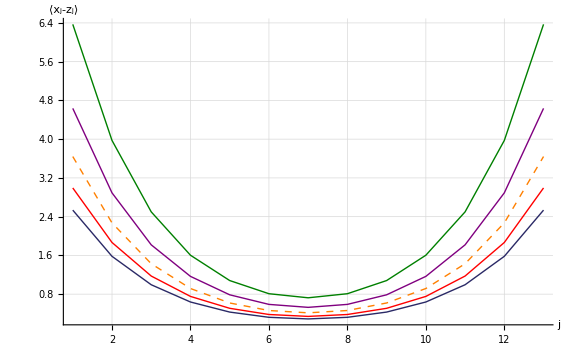
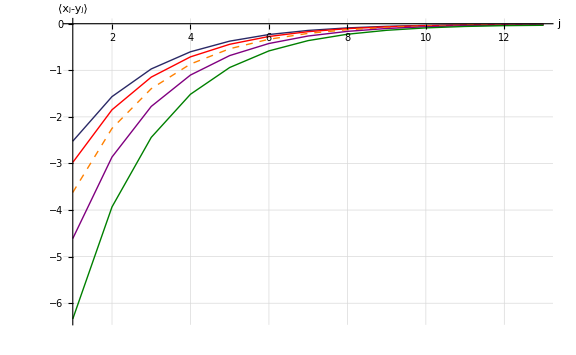

```mathematica
pos1=upos-2;
pos2=upos-1;
pos3=upos;
pos4=upos+1;
pos5=upos+2;

pxzpair=ListLinePlot[{xzpair[[pos1]],xzpair[[pos2]],xzpair[[pos3]],xzpair[[pos4]],xzpair[[pos5]]},ImageSize->Large,PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red},{Thick,Dashed,Orange},{Thick,Purple},{Thick,Darker[Green,0.5]}},PlotLegend->{Style["u="<>ToString[(pos1-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos2-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos3-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos4-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos5-1) Δ],FontSize->fs2]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],PlotRange->All,AxesOrigin->{1,0},AxesLabel->{Style["j",FontSize->fsAxesLabel],Style["⟨x_j-z_j⟩",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.55,LegendPosition->{0.9,-.2}];

pxypair=ListLinePlot[{xypair[[pos1]],xypair[[pos2]],xypair[[pos3]],xypair[[pos4]],xypair[[pos5]]},ImageSize->Large,PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red},{Thick,Dashed,Orange},{Thick,Purple},{Thick,Darker[Green,0.5]}},PlotLegend->{Style["u="<>ToString[(pos1-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos2-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos3-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos4-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos5-1) Δ],FontSize->fs2]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],PlotRange->All,AxesOrigin->{1,0},AxesLabel->{Style["j",FontSize->fsAxesLabel],Style["⟨x_j-y_j⟩",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.55,LegendPosition->{0.9,-.2}];

{pxzpair,pxypair}
```

Analysis

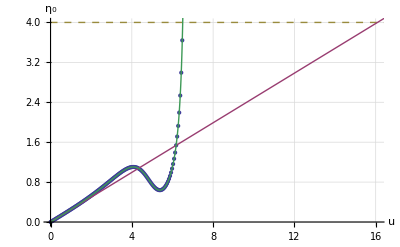

Interpolated Extension = 16.0869

Interpolated Extension = 16.0869\n

```mathematica
y[x_]:=Subscript[η, B]
MXDp1=Plot[y[x],{x,0,umax },PlotStyle->{ColorData[1,3],Dashed}];

MeanAxialDispDataRAW=Flatten[Transpose[Take[Transpose[xzpair],1]]];
maximumValue=Max[MeanAxialDispDataRAW];
positionOfMaximumValue=Flatten[Position[MeanAxialDispDataRAW,maximumValue]][[1]];

MeanAxialDispData = Table[{(i-1)Δ,MeanAxialDispDataRAW[[i]]},{i,1,positionOfMaximumValue}];
MXDp2=ListPlot[MeanAxialDispData];

model=a x  ;
MXDpara=FindFit[Take[MeanAxialDispData,10],model,{a},x];
mxd[u_]:=a u /.MXDpara


mxdInterFunc=Interpolation[MeanAxialDispData];
u=u0/.Quiet[FindRoot[mxd[u0]==Subscript[η, B],{u0,0}]];

MXDp3=Plot[mxd[u0],{u0,0,u+5},PlotStyle->{ColorData[1,2]}];
MXDp4=Plot[mxdInterFunc[x],{x,0,u},PlotRange->All,PlotStyle->ColorData[1,4]];

Show[{MXDp1,MXDp2,MXDp3,MXDp4},PlotRange->{{0,u},{0,Subscript[η, B]}},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["η_0",FontSize->fsAxesLabel]}]
Print["Interpolated Extension = ",u,"\n"]
```

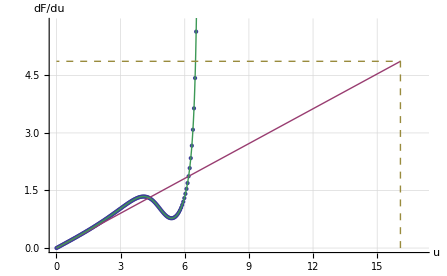

Interpolated Force = 4.86694

```mathematica
FreeEnergyMax=Max[Transpose[dFreeEnergy][[2]]];
positionOfFreeEnergyMax=Flatten[Position[dFreeEnergy,FreeEnergyMax]][[1]];
FreeEnergyData=Table[dFreeEnergy[[i]],{i,1,positionOfFreeEnergyMax}];
FEp1=ListPlot[FreeEnergyData];

model=a x  ;
FEpara=FindFit[Take[FreeEnergyData,10],model,{a},x];
dfe[u0_]:=a u0 /.FEpara
FEp2=Plot[dfe[u0],{u0,0,u},PlotStyle->{ColorData[1,2]}];

dfeInterFunc=Interpolation[FreeEnergyData];
F=dfe[u];


FEp3=Plot[dfeInterFunc[x],{x,0,u},PlotRange->{{0,u},{0,10}},PlotStyle->ColorData[1,4]];


fpos={{u,0},{u,F},{0,F}};
FEp4=ListLinePlot[fpos,PlotStyle->{ColorData[1,3],Dashed}];

Show[{FEp1,FEp2,FEp3,FEp4},PlotRange->{{0,u+1},{0,F+1}},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["dF/du",FontSize->fsAxesLabel]}]
Print["Interpolated Force = ",F,"\n"]
```

### Force-Extension

```mathematica
Fc=ToForceDimension[F];
U=ToDimension[u];

Print["\nDimensional Force = ",Fc pN,"\nDimensional Extension = ",U Å,"\n"]
Export["N"<>ToString[n]<>"_sim.data",{{n,Fc}},"Table"];
```

Dimensional Force = 280.349 pN
Dimensional Extension = 11.5674 Å